```mathematica
pos=FinancialData["NASDAQ:*","Lookup"];
```

```mathematica
Scrapping[stock_]:=Module[{data=stock},
returns=(Drop[data[[All,2]],1]-Drop[data[[All,2]],-1])/Drop[data[[All,2]],-1];
ShapiroWilkTest@returns
];
```

```mathematica
While[True,
curr = RandomChoice@pos;
Print[curr];
p = Scrapping[FinancialData[curr, "Jul. 1, 2017"]];
If[p > 0.5,Print[":)"];Break[]]]
```

NASDAQ:AMSWA

NASDAQ:AHPA

NASDAQ:FTXO

NASDAQ:PFIE

NASDAQ:UCTT

NASDAQ:BPTH

NASDAQ:PRAN

NASDAQ:CYTR

NASDAQ:FCAN

NASDAQ:AQXP

NASDAQ:SENEA

NASDAQ:RVSB

NASDAQ:SOHU

NASDAQ:SMMF

NASDAQ:GURE

NASDAQ:PDFS

NASDAQ:CRMT

NASDAQ:DWSN

NASDAQ:RVLT

NASDAQ:SGH

NASDAQ:AVDL

NASDAQ:MOSY

NASDAQ:PDBC

NASDAQ:QQQC

NASDAQ:ANGO

NASDAQ:DLBL

NASDAQ:GRMN

NASDAQ:FLL

NASDAQ:III

NASDAQ:ACWI

NASDAQ:LGCYP

NASDAQ:ICBK

NASDAQ:EBAY

NASDAQ:RVLT

NASDAQ:PYZ

NASDAQ:OBAS

NASDAQ:NYMTP

NASDAQ:CDL

NASDAQ:ASML

NASDAQ:ANCB

NASDAQ:WTFCM

NASDAQ:QCOM

NASDAQ:INFR

NASDAQ:SGOC

NASDAQ:ADRA

NASDAQ:DGICB

NASDAQ:DTUL

NASDAQ:PIRS

NASDAQ:AMRN

NASDAQ:ABEO

NASDAQ:PNTR

NASDAQ:BIOL

NASDAQ:OPK

NASDAQ:FNWB

NASDAQ:FIVN

NASDAQ:HBAN

NASDAQ:BLUE

NASDAQ:TPIC

NASDAQ:FAB

NASDAQ:RNEM

NASDAQ:AVHI

NASDAQ:WIX

NASDAQ:MDSO

NASDAQ:ANIK

NASDAQ:SYMC

NASDAQ:WWD

NASDAQ:ACLS

NASDAQ:AIRG

NASDAQ:PRMW

NASDAQ:COKE

NASDAQ:TTOO

NASDAQ:CVTI

NASDAQ:PIE

NASDAQ:HRTX

NASDAQ:MRCC

NASDAQ:CLLS

NASDAQ:NXEO

NASDAQ:PGNX

NASDAQ:GTYH

NASDAQ:MARPS

NASDAQ:FNWB

NASDAQ:SNOA

NASDAQ:NTRSP

NASDAQ:AMZN

NASDAQ:ONEQ

NASDAQ:GMLP

NASDAQ:SKIS

NASDAQ:BPRN

NASDAQ:MTEX

NASDAQ:LMB

NASDAQ:CODX

NASDAQ:RICK

NASDAQ:CDNA

NASDAQ:MNDO

NASDAQ:GFN

NASDAQ:JNP

NASDAQ:IIVI

NASDAQ:SPOK

NASDAQ:MSCC

NASDAQ:GWGH

NASDAQ:VBTX

NASDAQ:STLR

NASDAQ:RCII

NASDAQ:FNX

NASDAQ:DWLD

NASDAQ:STNL

NASDAQ:LECO

NASDAQ:STKS

NASDAQ:NAVI

NASDAQ:LINU

NASDAQ:SAGE

NASDAQ:FTLB

NASDAQ:AMNB

NASDAQ:GENY

NASDAQ:FDEF

NASDAQ:KBSF

NASDAQ:VCTR

NASDAQ:NBTB

:)

```mathematica
Length@FinancialData[curr,  "Jul. 1, 2017"]
```

218

```mathematica
FinancialData[curr,"Company"]
```

NBT Bancorp

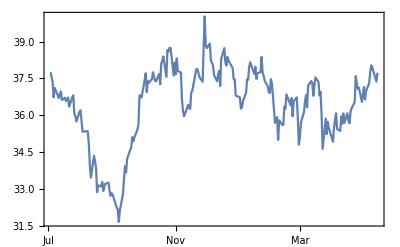

```mathematica
data =FinancialData[curr,"Jul. 1, 2017"];
DateListPlot[data]
```

```mathematica
Length[data]
```

218

```mathematica
data = data[[All,2]];
returns=(Drop[data,1]-Drop[data,-1])/Drop[data,-1];
```

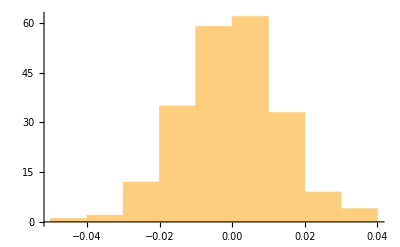

```mathematica
Histogram@returns
```

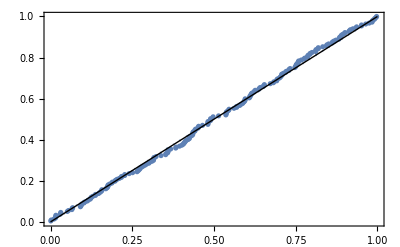

```mathematica
ProbabilityPlot@returns
```

```mathematica
ℋ=DistributionFitTest[returns,Automatic,"HypothesisTestData"];
ℋ["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 0.266319 | 0.709071
Baringhaus-Henze | 0.272274 | 0.621578
Cramér-von Mises | 0.0349088 | 0.767557
Jarque-Bera ALM | 1.92909 | 0.343331
Mardia Combined | 1.92909 | 0.343331
Mardia Kurtosis | 1.19461 | 0.23224
Mardia Skewness | 0.176135 | 0.674716
Pearson χ^2 | 9.20276 | 0.866679
Shapiro-Wilk | 0.995034 | 0.701435

```mathematica
ℋ["TestConclusion", "ShapiroWilk"]
```

The null hypothesis that the data is distributed according to the NormalDistribution[x,y] is not rejected at the 5 percent level based on the Shapiro-Wilk test.